## Toy nonlinear optimization problem

Minimize the functional

f[x]=1/2∫_0^1 (x-t)^2 ⅆt

subject to the constraint

x'=x(1-x)

x(0)=α

The constraint is the logistic equation, whose solution can be obtained by DSolve:

```mathematica
xSoln[α_,t_]=x[t]/.DSolve[{x'[t]== x[t](1-x[t]),x[0]==α},x[t],t][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(α ⅇ^t)/(-α+α ⅇ^t+1)

Now plug x(t) into the functional and evaluate, resulting in a function of α,

```mathematica
g[α_]=Integrate[1/2(xSoln[α,t]-t)^2,{t,0,1},Assumptions->{0<α<1}]
```

1/2 (((ⅇ-1) (α-1) α)/((ⅇ-1) α+1)+log((ⅇ-1) α+1)-2 (log((-ⅇ α+α-1)/(α-1))-2α/(α-1)+2(ⅇ α)/(α-1))+1/3)

We can plot this; the minimum is approximately 0.4

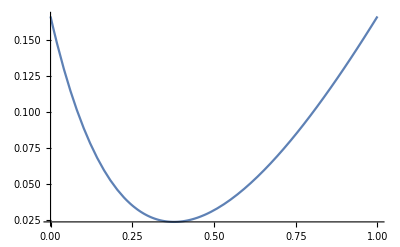

```mathematica
Plot[g[α],{α,0,1}]
```

Compute the minimum numerically

```mathematica
FindMinimum[g[α],{α,0.4}]
```

{0.0236299,{α→0.377541}}

The optimal design variable is α≈0.377541.